# AntonAntonov/ROCFunctions

Receiver Operating Characteristic (ROC) functions

## Paclet Manifest

"Documentation"

"English"

"Guides"

"Classifierevaluationfunctions.nb"DocumentationEnglishGuidesClassifierevaluationfunctions.nb

"ReferencePages"

"Symbols"

"ConfusionMatrixPlotFrame.nb"DocumentationEnglishReferencePagesSymbolsConfusionMatrixPlotFrame.nb

"ConfusionMatrixPlot.nb"DocumentationEnglishReferencePagesSymbolsConfusionMatrixPlot.nb

"ROCAssociationQ.nb"DocumentationEnglishReferencePagesSymbolsROCAssociationQ.nb

"ROCFunctions.nb"DocumentationEnglishReferencePagesSymbolsROCFunctions.nb

"ROCPlot.nb"DocumentationEnglishReferencePagesSymbolsROCPlot.nb

"ROCValues.nb"DocumentationEnglishReferencePagesSymbolsROCValues.nb

"ToClassifyROCCurvePlot.nb"DocumentationEnglishReferencePagesSymbolsToClassifyROCCurvePlot.nb

"ToROCAssociation.nb"DocumentationEnglishReferencePagesSymbolsToROCAssociation.nb

"Tutorials"

"Titanicdataclassifierevaluation.nb"DocumentationEnglishTutorialsTitanicdataclassifierevaluation.nb

"Kernel"

"ROCFunctions.wl"KernelROCFunctions.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

Receiver Operating Characteristic (ROC) functions and Confusion matrix plots.

### Details

Additional information about the paclet.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`ROCFunctions`"];
```

### Basic Examples

Here is a random dataset with columns "Actual" and "Predicted" that have the values "yes" and "now" and dataset's summary:

```mathematica
SeedRandom[9923];
dsRandomLabels=ResourceFunction["RandomTabularDataset"][{200,{"Actual","Predicted"}},"Generators"->{RandomChoice[{10,3}->{"yes","no"},#]&,{"yes","no"}}];
ResourceFunction["RecordsSummary"][dsRandomLabels]
```

{1 Actual
yes | 151
no | 49,2 Predicted
yes | 106
no | 94}

Here is a sample of the dataset:

```mathematica
RandomSample[dsRandomLabels,4]
```

-Graphics-

Here is the corresponding ROC association:

```mathematica
ToROCAssociation[{True,False},Normal[dsRandomLabels[All,"Actual"]],Normal[dsRandomLabels[All,"Predicted"]]]
```

<|TruePositive→0,FalsePositive→0,TrueNegative→0,FalseNegative→0|>

Here is the cross tabulation of the generated dataset:

```mathematica
ResourceFunction["CrossTabulate"][dsRandomLabels]
```

-Graphics-

Here is the corresponding sparse matrix:

```mathematica
mat=ResourceFunction["CrossTabulate"][dsRandomLabels,"Sparse"->True]
```

<|SparseMatrix→SparseArray[…],RowNames→{no,yes},ColumnNames→{no,yes}|>

Here is the corresponding confusion matrix plot:

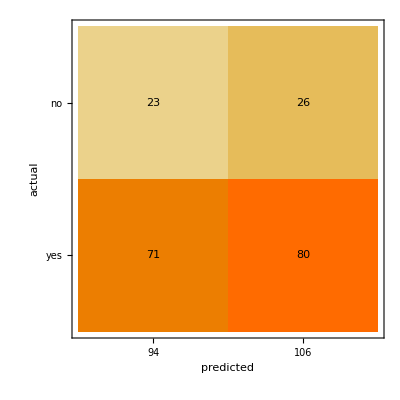

```mathematica
ConfusionMatrixPlotFrame[mat["SparseMatrix"],mat["RowNames"],mat["ColumnNames"]]
```

### Scope

Here are all ROC function names supported in the paclet:

```mathematica
ROCFunctions["FunctionNames"]
```

{TPR,TNR,SPC,PPV,NPV,FPR,FDR,FNR,ACC,AUROC,FOR,F1,MCC,Recall,Precision,Accuracy,Sensitivity}

Here are all properties of ROCFunctions:

```mathematica
ROCFunctions["Properties"]
```

{FunctionInterpretations,FunctionsAssociation,FunctionNames,Functions,Methods,Properties}

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-ROCFunctions-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Classification

Confusion matrix

Receiver Operating Characteristic

ROC

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Receiver operating characteristic - Wikipedia

### Links

MathematicaForPrediction/ROCFunctions.m at master · antononcube/MathematicaForPrediction · GitHub

ROCFunctions · PyPI

Raku Land - ML::ROCFunctions

### Compatibility

#### Wolfram Language Version

11.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.